## Выполнение расчетного задания по дисциплине Тепломассообмен в среде Mathematica 14 Студент: Жаркова А.Э. Группа: ТФ-13-22 Задача № 1 -Graphics- Рисунок(труба с изоляцией бетон/вата) -Graphics-

#### Данные из условия: d2=80(mm);δ=4(mm) - геометрия труб ; tAir=6 (°C)-температура воздуха;tLiquid1=200(°C)-температура горячей воды на входе (как t_ж1) ; p=5(MPa)- давление горячей воды;w=12(km/h) - скорость течения горячей воды; λMinWool=0.045(W/m*K);δMinWool=50(mm); tLiquid2=200-40=160(°C)-температура горячей воды на выходе(как t_ж2) ; λConcrete=1.28(W/m K);δConcrete=50(mm);ϵ=0.8-излучательная способность поверхности материала труб; α= 14.2(W/m^2K)-коэффициент теплоотдачи

```mathematica
d2=80*10^-3;δ=4*10^-3;tAir=6;tLiquid1=200;p=5*10^6;w=12/3.6;λMinWool=0.045;δMinWool=50*10^-3;tLiquid2=160;λConcrete=1.28;δConcrete=50*10^-3;
ϵ=0.8;
α=14.2;
```

#### Сталь берем нержавеющую, ее коэффициент теплопроводности λSteel (W/m K) берем как const в виду слабой зависимости от температуры:

```mathematica
λSteel=14.4 ;
```

#### Изобарную (p=5MPa)теплоемкость и плотность воды при tLiquid1 и tLiquid2 найдем через REFPROP: cp: tLiquid1=200 (°C) cp1=4.4753 (kJ/kg K) -Graphics-

#### tLiquid2=80 (°C) cp2=4.3194 (kJ/kg K) -Graphics- плотность: tLiquid1=200(°C) ρ1=867.22 (kg/m^3) -Graphics- tLiquid2=160 (°C) ρ2=909.99 (kg/m^3) -Graphics-

```mathematica
cp1=4.4753;cp2=4.3194 ;ρ1=867.22;ρ2=909.99;
```

#### Средняя удельная изобарная теплоемкость cpAverage(kJ/kg K)

```mathematica
cpAverage=(cp1+cp2)/2
```

4.39735

#### Средняя плотность воды ρAverage (kg/m^3)

```mathematica
ρAverage=(ρ1+ρ2)/2
```

888.605

#### Массовый расход воды G(kg/s)

```mathematica
G=π*((d2-2*δ)/2)^2*w*ρAverage
```

12.0599

#### Найдем диаметры d1, d3 (m)

```mathematica
d1=d2-2δ//N
```

0.072

```mathematica
d3=d2+2δ//N
```

0.088

#### Найдем линейный коэффициент теплопередачи для трубы с ватной изоляцией KlinearMinWool (W/m K)

```mathematica
KlinearMinWool=1/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λMinWool)*Log[d3/d2]+1/(α*d3))
```

0.351988

#### Применяя формулу Шухова найдем расстояние(длину трубы) на котором будет выполняться условие разности температур на входе и выходе в трубу с изоляцией из минеральной ваты:

```mathematica
First[NSolve[tLiquid2==tAir+(tLiquid1-tAir)*Exp[-KlinearMinWool/(G*cpAverage*1000)*π*x],x]]
```

{x→11073.6}

#### Таким образом длина трубы равна 11073.636 m)

```mathematica
L=11073.6362;
```

#### Найдем линейный коэффициент теплопередачи для трубы с бетонной изоляцией KlinearConcrete (W/m K)

```mathematica
KlinearConcrete=1/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/(α*d3))
```

0.549681

#### По формуле Шухова найдем температуру на выходе из трубы с бетонной изоляцией:

```mathematica
t[x_,k_]:=tAir+(tLiquid1-tAir)*Exp[-k/(G*cpAverage*1000)*π*x]
```

```mathematica
t[L,KlinearConcrete]
```

141.269

#### Найдем линейный коэффициент теплопередачи для трубы без изоляции KlinearRaw (W/m K)

```mathematica
KlinearRaw=1/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(α*d3))
```

0.561166

#### По формуле Шухова найдем температуру на выходе из трубы без изоляции:

```mathematica
t[L,KlinearRaw]
```

140.254

#### Функция теплового потока и плотности теплового потока :

```mathematica
Q[x_,k_]:=k*π*(t[x,k]-tAir)*x;
qLinear[x_,k_]:=k*π*(t[x,k]-tAir);
```

#### Тепловой поток Q(W) и его линейная плотность qLinear(W/m) для голой трубы:

```mathematica
Q[L,KlinearRaw]
```

2.62094×10^6

```mathematica
qLinear[L,KlinearRaw]
```

236.683

#### Тепловой поток Q(W) и его линейная плотность qLinear(W/m) для трубы с бетонной изоляцией:

```mathematica
Q[L,KlinearConcrete]
```

2.58672×10^6

```mathematica
qLinear[L,KlinearConcrete]
```

233.593

#### Тепловой поток Q(W) и его линейная плотность qLinear(W/m) для трубы с ватной изоляцией:

```mathematica
Q[L,KlinearMinWool]
```

1.88577×10^6

```mathematica
qLinear[L,KlinearMinWool]
```

170.294

### Произведем расчеты по другому:

```mathematica
qLinearAdditional[k_]:=k*π*((tLiquid1+tLiquid2)/2-tAir)
```

#### Запишем баланс энергий: Q=qLinear*L=G*cpAverage*(tLiquid1-tLiquid2)=π *(d1/2)^2*w*cpAverage*ρAverage*(tLiquid1-tLiquid2),отсюда можно найти L:

```mathematica
NSolve[qLinearAdditional[KlinearMinWool]*x==π*(d1/2)^2*w*cpAverage*1000*ρAverage*(tLiquid1-tLiquid2),x]
```

{{x→11024.7}}

#### Таким образом длина трубы по этому способу равна Ladditional(m)

```mathematica
Ladditional=11024.696;
```

#### Выразим tLiquid2 из линейной плотности теплового потока как переменную :

```mathematica
Solve[k*π*((tLiquid2asVariable+tLiquid1)/2-tAir)*x==π*(d1/2)^2*w*cpAverage*1000*ρAverage*(tLiquid1-tLiquid2asVariable),tLiquid2asVariable]
```

{{tLiquid2asVariable→(1.06063×10^7-295.31 k x)/(53031.4+1.5708 k x)}}

```mathematica
tLiquid2asVariable[k_,x_]:=(1.0606288*10^7-295.3097* k *x)/(53031.4383+1.570796* k *x)
```

#### Теперь найдем температуры на выходе из трубы с бетонной изоляцией и трубы без изоляции. Бетонная изоляция:

```mathematica
tLiquid2asVariable[KlinearConcrete,Ladditional]
```

140.953

#### Голая труба:

```mathematica
tLiquid2asVariable[KlinearRaw,Ladditional]
```

139.91

#### Изобразим функциональные зависимости температуры жидкости в точке χ, где χ-обобщенное расстояние(длина трубы)

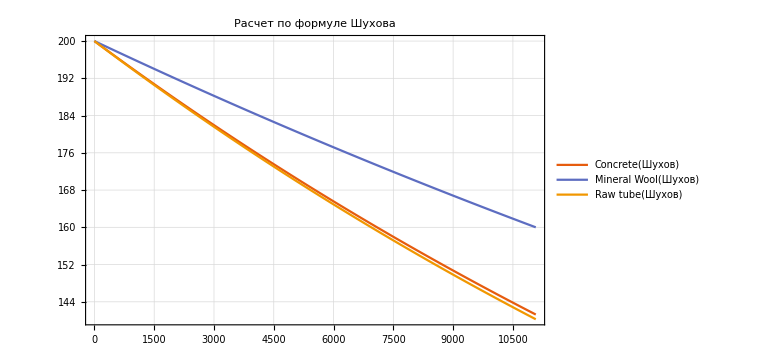

```mathematica
Plot[{t[χ,KlinearConcrete],t[χ,KlinearMinWool],t[χ,KlinearRaw]},{χ,0,L},PlotLabel->"Расчет по формуле Шухова",PlotTheme->"Scientific",PlotLegends->{"Concrete(Шухов)","Mineral Wool(Шухов)","Raw tube(Шухов)"},ImageSize->Large,GridLines->Automatic]
```

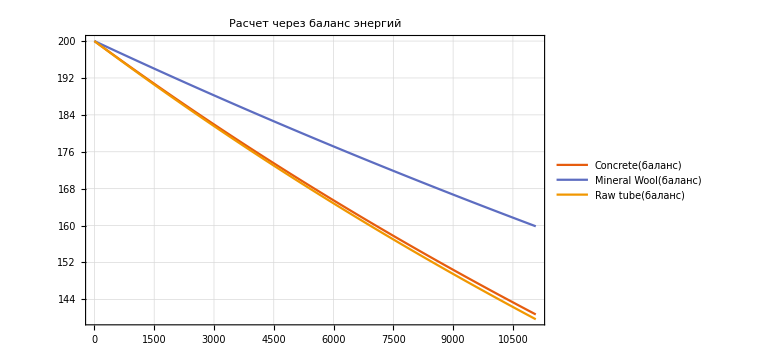

```mathematica
Plot[{tLiquid2asVariable[KlinearConcrete,χ],tLiquid2asVariable[KlinearMinWool,χ],tLiquid2asVariable[KlinearRaw,χ]},{χ,0,L},PlotLabel->"Расчет через баланс энергий",PlotTheme->"Scientific",PlotLegends->{"Concrete(баланс)","Mineral Wool(баланс)","Raw tube(баланс)"},ImageSize->Large,GridLines->Automatic]
```

#### Сопоставим функции температур в одной системе координат:

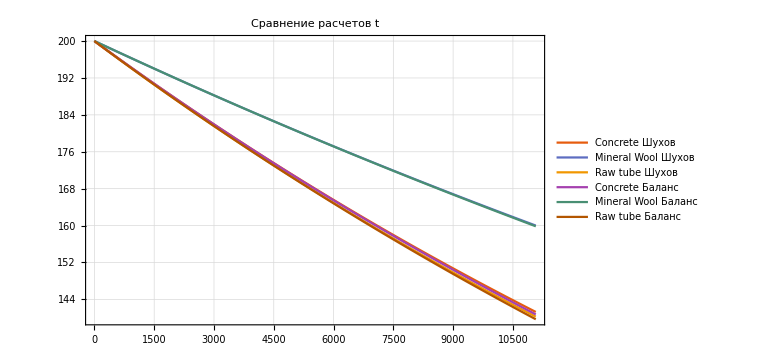

```mathematica
Plot[{t[χ,KlinearConcrete],t[χ,KlinearMinWool],t[χ,KlinearRaw],tLiquid2asVariable[KlinearConcrete,χ],tLiquid2asVariable[KlinearMinWool,χ],tLiquid2asVariable[KlinearRaw,χ]},{χ,0,L},PlotLabel->"Сравнение расчетов t",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Баланс","Mineral Wool Баланс","Raw tube Баланс"},ImageSize->Large,GridLines->Automatic]
```

#### Точно так же изобразим функции линейных плотностей тепловых потоков. Для начала введем функцию линейной плотности теплового потока при расчете методом баланса энергий:

```mathematica
qLinearAdditionalFunction[k_]:=k*π*((tLiquid1-tLiquid2)/2-tAir)
```

#### Покажем графики линейных плотностей тепловых потоков в одной координатной плоскости ql(W/m):

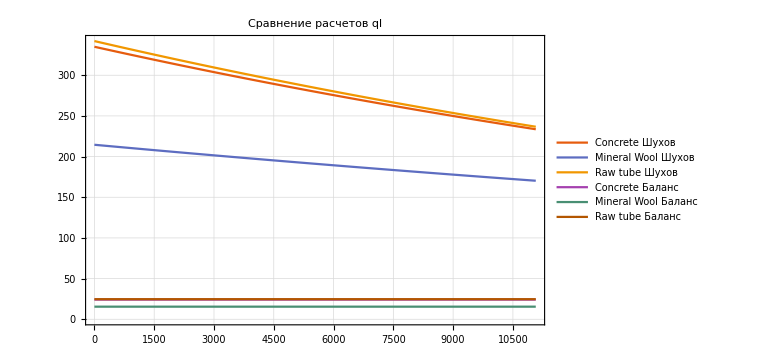

```mathematica
Plot[{qLinear[χ,KlinearConcrete],qLinear[χ,KlinearMinWool],qLinear[χ,KlinearRaw],qLinearAdditionalFunction[KlinearConcrete],qLinearAdditionalFunction[KlinearMinWool],qLinearAdditionalFunction[KlinearRaw]},{χ,0,L},PlotLabel->"Сравнение расчетов ql",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Баланс","Mineral Wool Баланс","Raw tube Баланс"},ImageSize->Large,GridLines->Automatic]
```

#### Теперь построим поверхностные плотности тепловых потоков qc (W/m^2):

```mathematica
qcShuhov[x_,k_]:=qLinear[x,k]/(π*d1);qcBalance[k_]:=qLinearAdditionalFunction[k]/(π*d1);
```

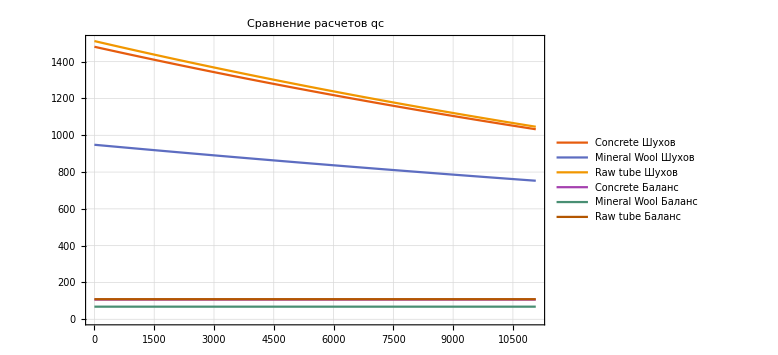

```mathematica
Plot[{qcShuhov[χ,KlinearConcrete],qcShuhov[χ,KlinearMinWool],qcShuhov[χ,KlinearRaw],qcBalance[KlinearConcrete],qcBalance[KlinearMinWool],qcBalance[KlinearRaw]},{χ,0,L},PlotLabel->"Сравнение расчетов qc",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Баланс","Mineral Wool Баланс","Raw tube Баланс"},ImageSize->Large,GridLines->Automatic]
```

#### Найдем среднее значение линейной плотности теплового потока(W/m):

```mathematica
qLinearAverageWithoutInsulation=(qLinear[0,KlinearRaw]+qLinear[L,KlinearRaw])/2
```

289.348

```mathematica
qLinearAverageConcreteInsulation=(qLinear[0,KlinearConcrete]+qLinear[L,KlinearConcrete])/2
```

284.303

```mathematica
qLinearAverageMinWoolInsulation=(qLinear[0,KlinearMinWool]+qLinear[L,KlinearMinWool])/2
```

192.41

#### Среднее значение температуры на поверхности труб:

```mathematica
NSolve[{qLinearAverageWithoutInsulation==π*(twWithoutIns-tAir)/(1/(α*d2)),qLinearAverageConcreteInsulation==π*(twConcreteIns-tAir)/(1/(α*d3)),qLinearAverageMinWoolInsulation==π*(twMinWoolIns-tAir)/(1/(α*d3))},{twWithoutIns,twConcreteIns,twMinWoolIns}]
```

{{twWithoutIns→87.076,twConcreteIns→78.4204,twMinWoolIns→55.0124}}

```mathematica
twWithoutIns=49.902233;twConcreteIns=47.0828314;twMinWoolIns=38.209809;
```

#### Учтем излучение σ- константа Стефана-Больцмана(W/m^2 K^4)

```mathematica
σ=5.671*10^-8;
```

#### Переведем температуры на поверхности труб и температуру воздуха в абсолютные единицы(Кельвины)

```mathematica
TwWithoutIns=twWithoutIns+273.15;TwConcreteIns=twConcreteIns+273.15;TwMinWoolIns=twMinWoolIns+273.15;Tair=tAir+273.15;
```

#### Найдем результирующую плотность потока излучения Eres(W/m^2):

```mathematica
EresMinWool=ϵ*σ*(TwMinWoolIns^4-Tair^4)
```

150.897

```mathematica
EresConcrete=ϵ*σ*(TwConcreteIns^4-Tair^4)
```

201.618

```mathematica
EresWithoutIns=ϵ*σ*(TwWithoutIns^4-Tair^4)
```

218.643

#### Найдем эквивалентный коэффициент теплоотдачи излучением αEqv (W/m^2K):

```mathematica
αEqvMinWool=EresMinWool/(TwMinWoolIns-Tair)
```

4.6848

```mathematica
αEqvConcrete=EresConcrete/(TwConcreteIns-Tair)
```

4.90759

```mathematica
αEqvWithoutIns=EresWithoutIns/(TwWithoutIns-Tair)
```

4.98022

```mathematica
MradMinWool=1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λMinWool)*Log[d3/d2]+1/((α+αEqvMinWool)*d3)
```

2.64249

```mathematica
MradConcrete=1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/((α+αEqvConcrete)*d3)
```

1.6137

```mathematica
MradWithoutIns=1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/((α+αEqvWithoutIns)*d3)
```

1.57422

```mathematica
P=(d1/2)^2*w*ρAverage*cpAverage*1000
```

16880.4

```mathematica
tLiquid2RadiationVariable[M_,x_]:=(2*P*M*tLiquid1+2*tAir*x - tLiquid1*x)/(x+2*P*M)
```

#### Линейная плотность потока излучения для трубы с ватной изоляцией:

```mathematica
qLinearRadiationMinWool[x_]:=π*((tLiquid1+tLiquid2RadiationVariable[MradMinWool,x])/2-tAir)/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/((α+αEqvMinWool)*d3))
```

#### Из баланса энергий найдем длину трубы:

```mathematica
NSolve[((tLiquid1+tLiquid2)/2-tAir)/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/((α+αEqvMinWool)*d3))*Len ==π*(d1/2)^2*w*ρAverage*cpAverage*1000*(tLiquid1-tLiquid2),Len]
```

{{Len→19758.3}}

#### Если учитывать излучение тогда длина трубы будет другой(m):

```mathematica
LwithRadiation=19758.345;
```

#### Линейная плотность потока излучения трубы с ватной изоляцией:(W/m)

```mathematica
qLinearRadiationMinWool[LwithRadiation]
```

307.865

#### Для трубы без изоляции:(W/m^2)

```mathematica
qLinearRadiationWithoutIns[x_]:=π*((tLiquid1+tLiquid2RadiationVariable[MradWithoutIns,x])/2-tAir)/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/((α+αEqvWithoutIns)*d3))
```

```mathematica
qLinearRadiationWithoutIns[LwithRadiation]
```

282.232

```mathematica
tLiquid2RadiationVariableWithoutIns=tLiquid2RadiationVariable[MradWithoutIns,LwithRadiation]
```

94.8465

#### Для трубы с изоляцией из бетона:

```mathematica
qLinearRadiationConcrete[x_]:=π*((tLiquid1+tLiquid2RadiationVariable[MradConcrete,x])/2-tAir)/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/((α+αEqvConcrete)*d3))
```

```mathematica
qLinearRadiationConcrete[LwithRadiation]
```

277.165

```mathematica
tLiquid2RadiationVariable[MradConcrete,LwithRadiation]
```

96.7346

#### Рассчитаем потери теплоты:

```mathematica
QradConcrete[x_]:=qLinearRadiationConcrete[x]*x;
QradMinWool[x_]:=qLinearRadiationMinWool[x]*x;
QradWithoutIns[x_]:=qLinearRadiationWithoutIns[x]*x;
```

#### Потери теплоты в трубе с бетонной изоляцией:(W)

```mathematica
QradConcrete[LwithRadiation]
```

5.47631×10^6

#### Потери теплоты в трубе с ватной изоляцией:(W)

```mathematica
QradMinWool[LwithRadiation]
```

6.08291×10^6

```mathematica
QradWithoutIns[LwithRadiation]
```

5.57644×10^6

#### Сравним расчеты температуры(Шухов/Излучение):

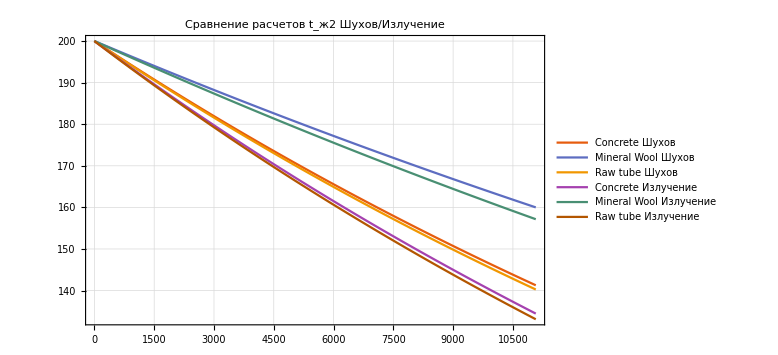

```mathematica
Plot[{t[χ,KlinearConcrete],t[χ,KlinearMinWool],t[χ,KlinearRaw],tLiquid2RadiationVariable[MradConcrete,χ],tLiquid2RadiationVariable[MradMinWool,χ],tLiquid2RadiationVariable[MradWithoutIns,χ]},{χ,0,L},PlotLabel->"Сравнение расчетов t_(:04362) Шухов/Излучение",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Излучение","Mineral Wool Излучение","Raw tube Излучение"},ImageSize->Large,GridLines->Automatic]
```

#### Сравним расчеты линейной плотности потоков тепла/излучения(Шухов/Излучение):

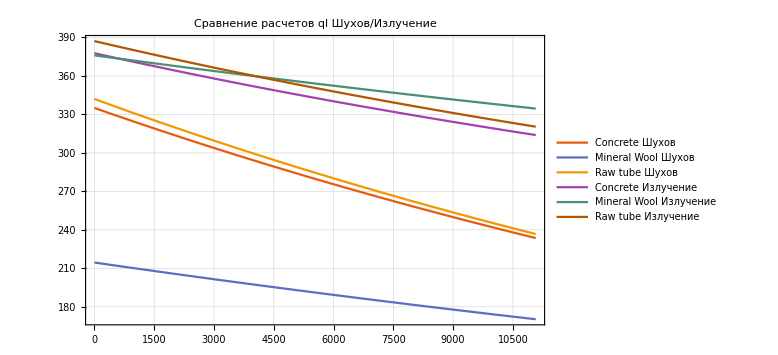

```mathematica
Plot[{qLinear[χ,KlinearConcrete],qLinear[χ,KlinearMinWool],qLinear[χ,KlinearRaw],qLinearRadiationConcrete[χ],qLinearRadiationMinWool[χ],qLinearRadiationWithoutIns[χ]},{χ,0,L},PlotLabel->"Сравнение расчетов ql Шухов/Излучение",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Излучение","Mineral Wool Излучение","Raw tube Излучение"},ImageSize->Large,GridLines->Automatic]
```

#### Соберем все результаты выше воедино. Способ основанный на формуле Шухова. Температуры жидкости на выходе(°C):(порядок:бетон,вата,без изоляции)

```mathematica
t[L,KlinearConcrete]
```

141.269

```mathematica
t[L,KlinearMinWool]
```

160.

```mathematica
t[L,KlinearRaw]
```

140.254

#### Тепловой поток(W):(порядок:бетон,вата,без изоляции)

```mathematica
Q[L,KlinearConcrete]
```

2.58672×10^6

```mathematica
Q[L,KlinearMinWool]
```

1.88577×10^6

```mathematica
Q[L,KlinearRaw]
```

2.62094×10^6

#### Способ основанный на методе баланса энергии. Температуры жидкости на выходе(°C):(порядок:бетон,вата,без изоляции)

```mathematica
tLiquid2asVariable[KlinearConcrete,Ladditional]
```

140.953

```mathematica
tLiquid2asVariable[KlinearMinWool,Ladditional]
```

160.

```mathematica
tLiquid2asVariable[KlinearRaw,Ladditional]
```

139.91

#### Тепловой поток(W):(порядок:бетон,вата,без изоляции)

```mathematica
Qadditional[k_,x_]:=qLinear[x,k]*x;
```

```mathematica
Qadditional[KlinearConcrete,Ladditional]
```

2.57939×10^6

```mathematica
Qadditional[KlinearMinWool,Ladditional]
```

1.87935×10^6

```mathematica
Qadditional[KlinearRaw,Ladditional]
```

2.61361×10^6

#### Способ с учетом излучения.Температуры жидкости на выходе(°C):(порядок:бетон,вата,без изоляции)

```mathematica
tLiquid2RadiationVariable[MradConcrete,LwithRadiation]
```

96.7346

```mathematica
tLiquid2RadiationVariable[MradMinWool,LwithRadiation]
```

129.649

```mathematica
tLiquid2RadiationVariable[MradWithoutIns,LwithRadiation]
```

94.8465

#### Поток излучения(W):(порядок:бетон,вата,без изоляции)

```mathematica
QradConcrete[LwithRadiation]
```

5.47631×10^6

```mathematica
QradMinWool[LwithRadiation]
```

6.08291×10^6

```mathematica
QradWithoutIns[LwithRadiation]
```

5.57644×10^6

#### Найдем критический диаметр при бетонной и ватной изоляциях

```mathematica
d2//N
```

0.08

```mathematica
dCriticalConcrete=d2+(2λConcrete)/α
```

0.260282

#### Мы не дошли до критического диаметра для трубы с бетонной изоляцией.

```mathematica
dCriticalMinWool=d2+(2λMinWool)/α
```

0.086338

#### Мы перешли критический диаметр для трубы с ватной изоляцией. Вывод: Тепло от теплоносителя лучше всего сохраняет труба с ватной изоляцией. На втором месте бетон. На третьем- труба без изоляции.